# Project report

## Carrier gas flow measurement

D Malan

Department of Chemistry
University of Pretoria

11 January 2020

## Introduction

We need to have a measure of the carrier gas flow in the fast GC column. The convention is to use average linear velocity, which is measured by dividing the length of the column by the retention time of an unretained compound. In the fast GC this is not a realistic, simple solution, because the void time is to short to measure conveniently with a stopwatch: by the time the syringe is removed from the inlet the compound is already eluting. I therefore used the installation of a new column as an opportunity to do a gas flow calibration.

## Experimental

Using different settings on the pressure regulator of the GC inlet gas pressure, I measured the volumetric flow through a 1-metre length of column using a bubble flow meter.

## Calculations

```mathematica
data = Import["C:\\Users\\fskdm\\My PhD\\Projects\\2019_12_20_PhD_Last_Project\\2019_12_17_Flow_measurement.xlsx"];
```

```mathematica
TableForm[data]
```

Head pressure (psi)
Volume (ml)
Time (s)
Time (min)
Flow (ml/min) | 8.
2.
11.2
0.186667
10.7143 | 8.
2.
11.11
0.185167
10.8011 | 8.
1.5
8.31
0.1385
10.8303 | 8.
2.
10.99
0.183167
10.919 | 12.
2.
3.58
0.0596667
33.5196 | 12.
2.
3.63
0.0605
33.0579 | 12.
2.
3.61
0.0601667
33.241 | 12.
2.
3.7
0.0616667
32.4324 | 12.
2.
3.75
0.0625
32. | 16.
2.
2.13
0.0355
56.338 | 16.
10.
9.91
0.165167
60.5449 | 16.
10.
11.88
0.198
50.5051 | 16.
2.
2.07
0.0345
57.971 | 16.
2.
1.99
0.0331667
60.3015 | 20.
8.
5.31
0.0885
90.3955 | 20.
8.
5.38
0.0896667
89.2193 | 20.
8.
5.33
0.0888333
90.0563 | 20.
8.
5.32
0.0886667
90.2256 | 20.
10.
6.73
0.112167
89.153 | 7.
1.
8.79
0.1465
6.82594 | 7.
1.
8.55
0.1425
7.01754 | 7.
1.
8.46
0.141
7.0922 | 7.
1.
8.46
0.141
7.0922 | 7.
1.
8.35
0.139167
7.18563
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
line = Fit[data[[1]][[2;;,{1,5}]], {1,x},x]
```

-39.7755+6.29333 x

## Results & Discussion

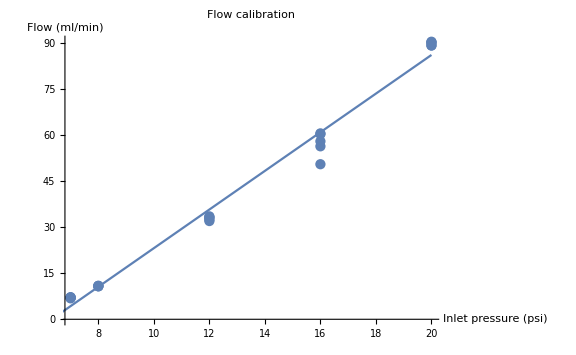

```mathematica
Show[
	ListPlot[data[[1]][[2;;,{1,5}]]
, PlotLabel-> "Flow calibration"
,AxesLabel->{"Inlet pressure (psi)","Flow (ml/min)"} 
, ImageSize->Large]
	, Plot[line, {x, 0, 20}]
]
```

The graph shows how the flow varies with head pressure. Because of the shortness of the column the flow is very high for head pressures that would be considered quite moderate in normal GC.

## Conclusion

The flow data that was collected will be useful in predicting the carrier gas flow in the SFC×GC.